```mathematica
?Random
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

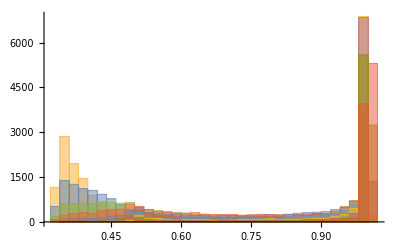

```mathematica
qs=(s=#;
lognorms=Exp[InverseCDF[NormalDistribution[0,s],Random[]]]&/@Range[3]&/@Range[10000];
Total[#]/Total[Sqrt/@#]^2&/@lognorms)&/@(10^Range[0,2,.2]);
```

```mathematica
?Hue
```

Hue[h] is a graphics directive which specifies that objects which follow are to be displayed, in a color corresponding to hue h. 
Hue[h,s,b] specifies colors in terms of hue, saturation, and brightness. 
Hue[h,s,b,a] specifies opacity a.

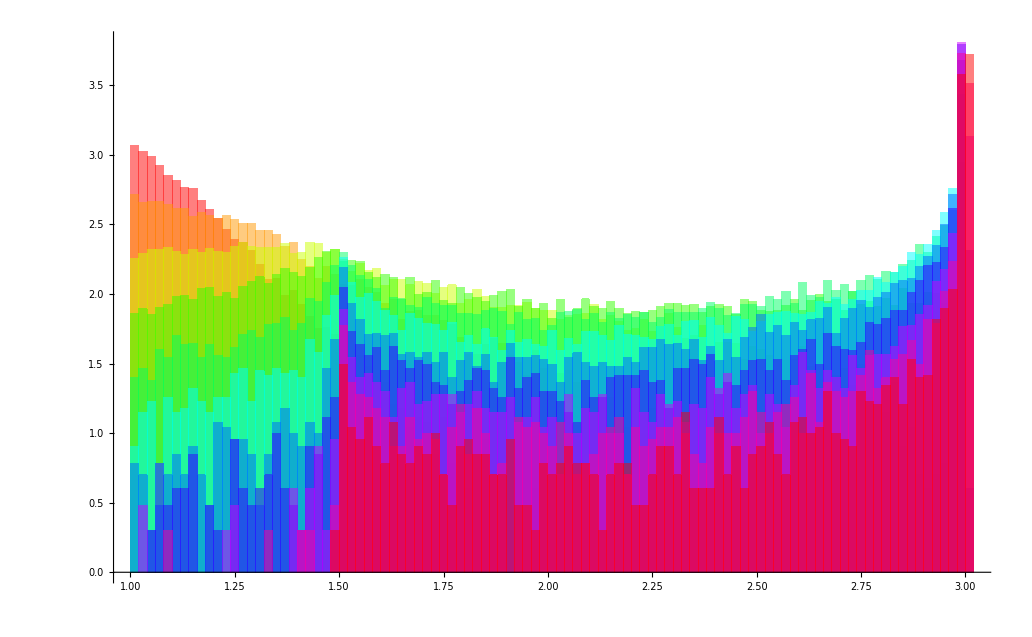

```mathematica
Histogram[3qs,60,Log10/@#2&,ChartStyle->Hue/@Range[0,1,.1]]
```

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

```mathematica
q2s=(s=#;
lognorms=Exp[InverseCDF[NormalDistribution[0,s],Random[]]]&/@Range[3]&/@Range[10000];
Total[#]/Total[Sqrt/@#]^2&/@lognorms)&/@{100};
```

```mathematica
q2s//Dimensions
```

{1,10000}

```mathematica
Exp[10^Range[0,2,.2]]
```

{2.71828,4.87877,12.3282,53.5744,549.81,22026.5,7.64018×10^6,8.10931×10^10,1.94794×10^17,2.52423×10^27,2.68812×10^43}